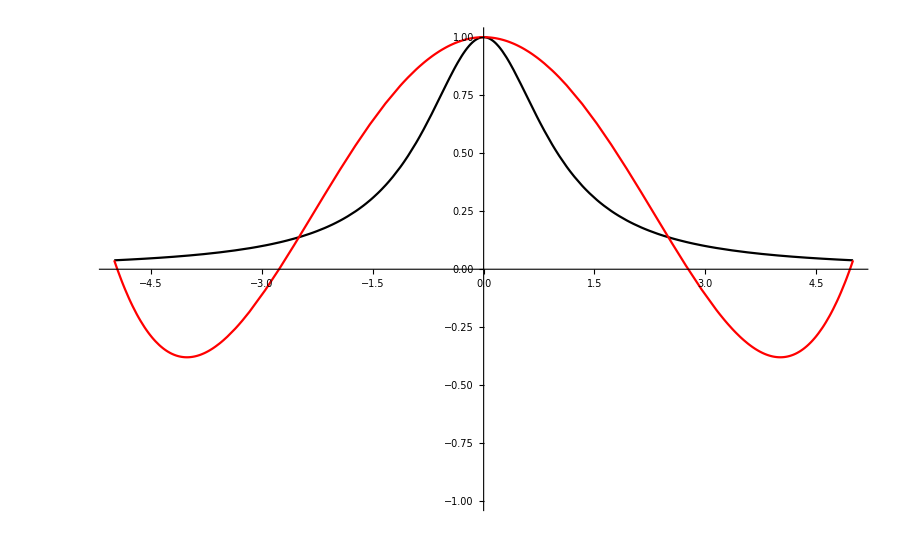

```mathematica
f=1/(1+x^2);
a=-5.;
b=5;
n=4;
xj=Table[a+j(b-a)/n,{j,0,n}];
L=Table[(∏_(k=0)^(j-1) (x-xj[[k+1]])/(xj[[j+1]]-xj[[k+1]]))(∏_(k=j+1)^n (x-xj[[k+1]])/(xj[[j+1]]-xj[[k+1]])),{j,0,n}];
p=∑_(j=0)^n (f/.x->xj[[j+1]]) L[[j+1]];
Plot[{f,p},{x,a,b},PlotStyle->{RGBColor[0,0,0],RGBColor[1,0,0]},PlotRange->{-1,1}]
```

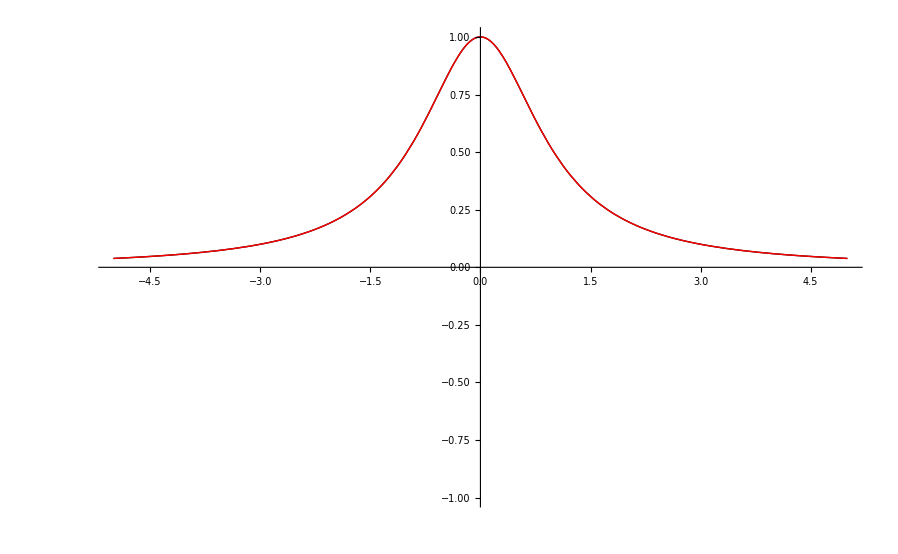

```mathematica
f=1/(1+x^2);
a=-5.;
b=5;
n=64;
xj=Sort[(b-a)(Table[Cos[((2j+1)π)/(2(n+1))],{j,0,n}]+1)/2+a,Less];
L=Table[(∏_(k=0)^(j-1) (x-xj[[k+1]])/(xj[[j+1]]-xj[[k+1]]))(∏_(k=j+1)^n (x-xj[[k+1]])/(xj[[j+1]]-xj[[k+1]])),{j,0,n}];
p=∑_(j=0)^n (f/.x->xj[[j+1]]) L[[j+1]];
Plot[{f,p},{x,a,b},PlotStyle->{RGBColor[0,0,0],RGBColor[1,0,0]},PlotRange->{-1,1}]
```